Graphs
Original

```mathematica
ListPlot3D[Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\COVARIANCE\\cograph.dat", "Data"], InterpolationOrder->1]
```

-Graphics3D-

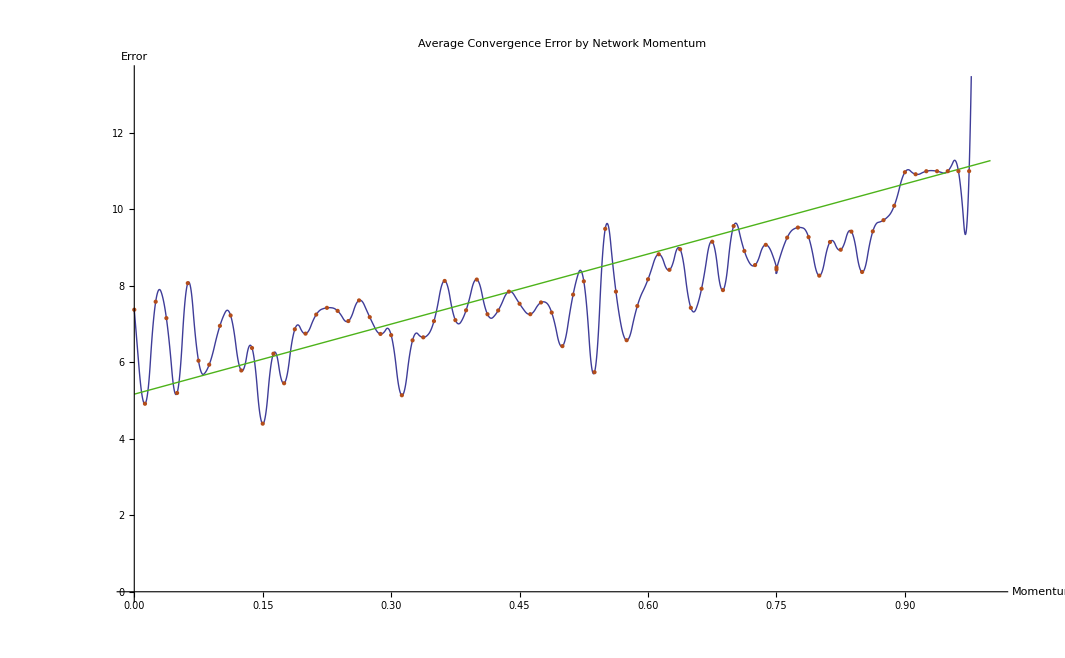

```mathematica
data = Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\MM\\mmgraph.dat", "Data"];
Show[ListLinePlot[data, InterpolationOrder->2],
Plot[Evaluate[Fit[data, {1,x}, x]],  {x,0,1},
 PlotStyle->{RGBColor[0.3,0.7,0.1]}],
ListPlot[data, PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{
Style["Momentum", FontSize->21],
Style["Error", FontSize->21]},
         PlotLabel->Style["Average Convergence Error by Network Momentum", FontSize->36]]
```

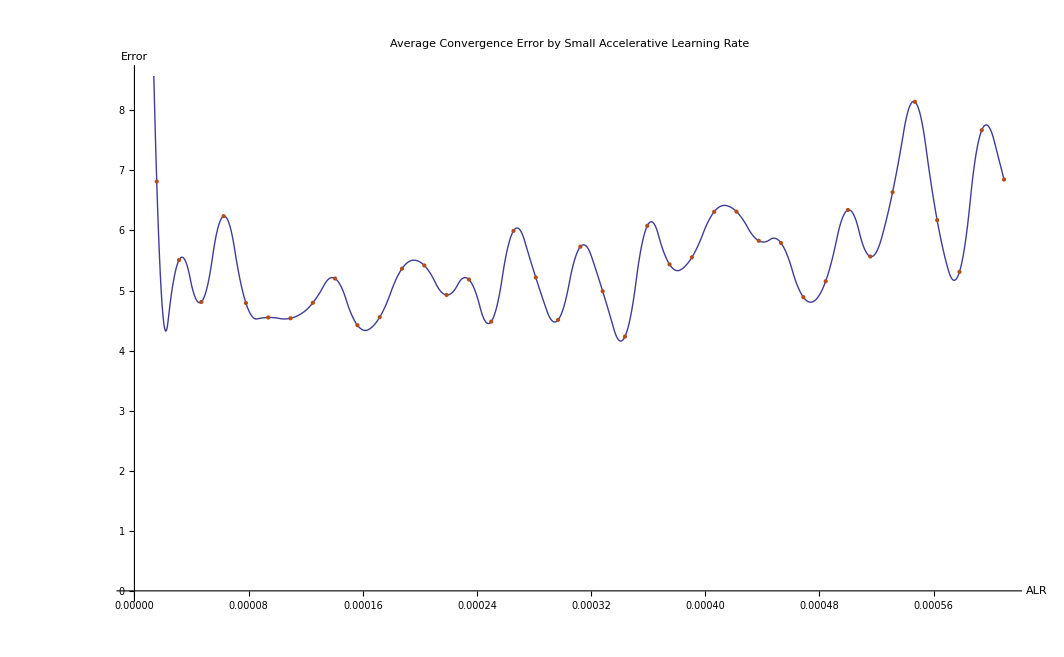

```mathematica
data2 = Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\Smallest\\smallgraph.dat", "Data"];
Show[ListLinePlot[data2, InterpolationOrder->2],
ListPlot[data2, PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{
Style["ALR", FontSize->21],
Style["Error", FontSize->21]},
         PlotLabel->Style["Average Convergence Error by Small Accelerative Learning Rate", FontSize->36]]
```

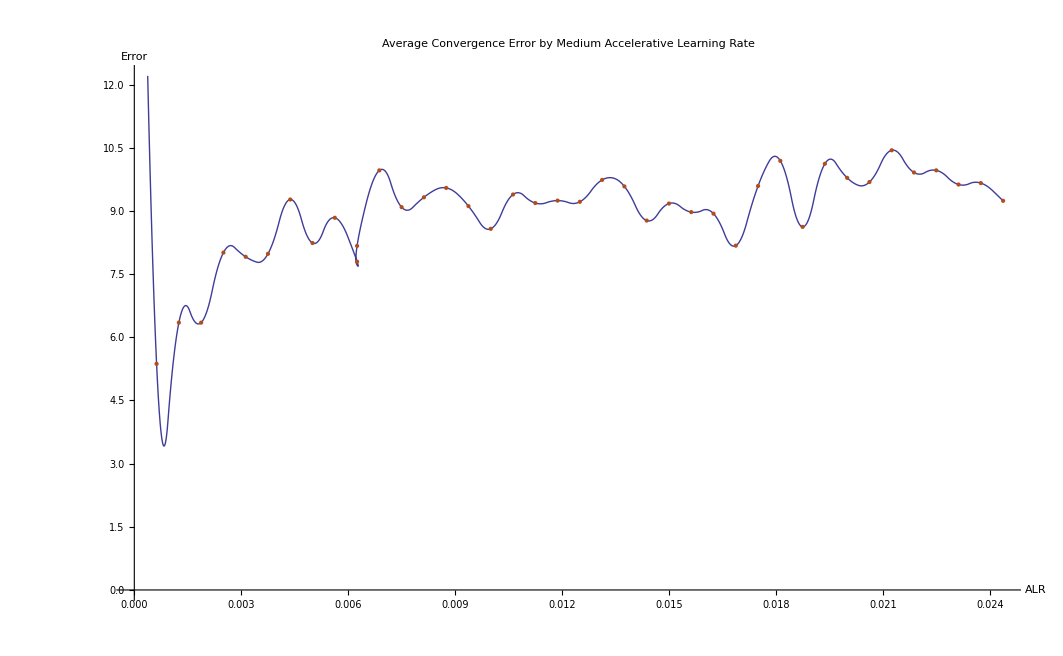

```mathematica
data3 = Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\Medium\\mediumgraph.dat", "Data"];
Show[ListLinePlot[data3, InterpolationOrder->2],
ListPlot[data3, PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{
Style["ALR", FontSize->21],
Style["Error", FontSize->21]},
         PlotLabel->Style["Average Convergence Error by Medium Accelerative Learning Rate", FontSize->36]]
```

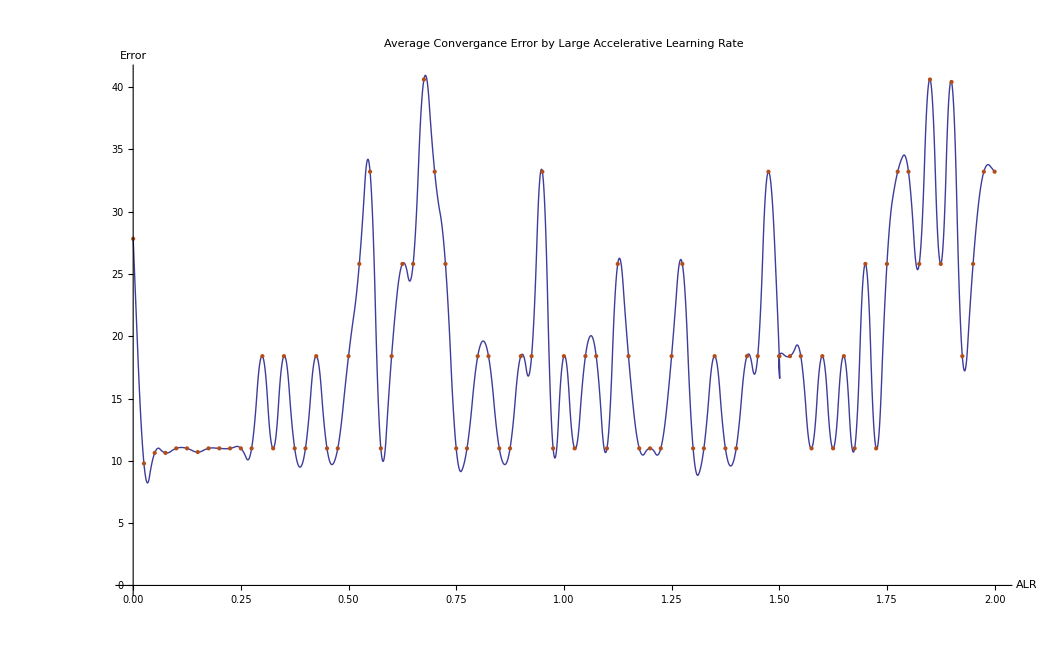

```mathematica
data = Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\Large\\broadgraph.dat", "Data"];
Show[ListLinePlot[data, InterpolationOrder->2],
ListPlot[data, PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{
Style["ALR", FontSize->21],
Style["Error", FontSize->21]},
         PlotLabel->Style["Average Convergance Error by Large Accelerative Learning Rate", FontSize->36]]
```

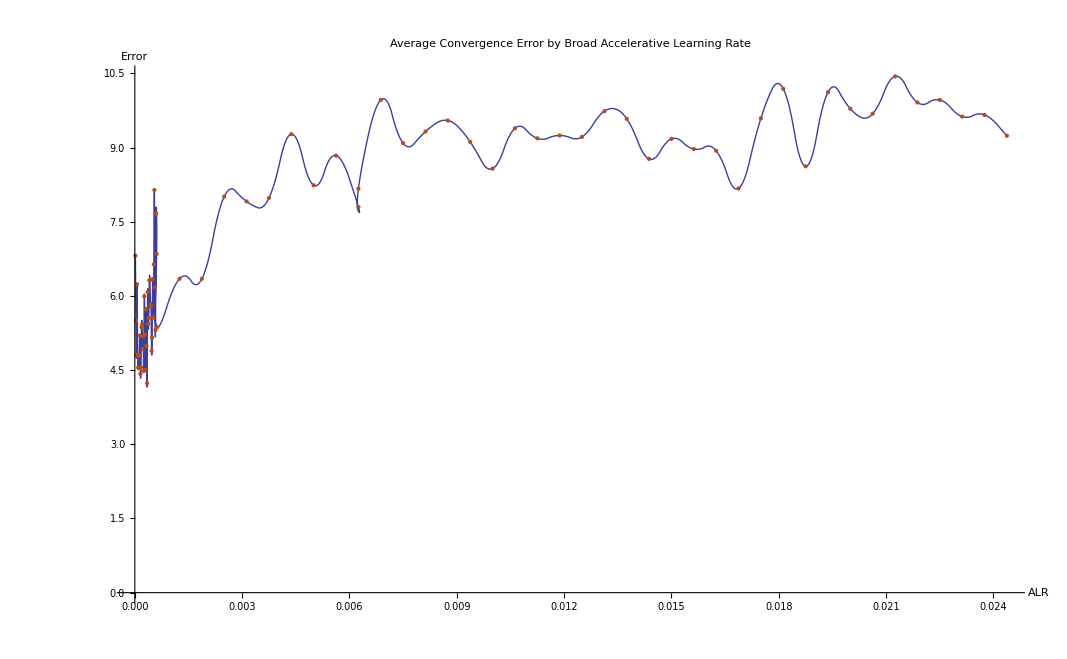

```mathematica
data = Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\broad\\broadgraph.dat", "Data"];
Show[ListLinePlot[data, InterpolationOrder->2],
ListPlot[data, PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{
Style["ALR", FontSize->21],
Style["Error", FontSize->21]},
         PlotLabel->Style["Average Convergence Error by Broad Accelerative Learning Rate", FontSize->36]]
```

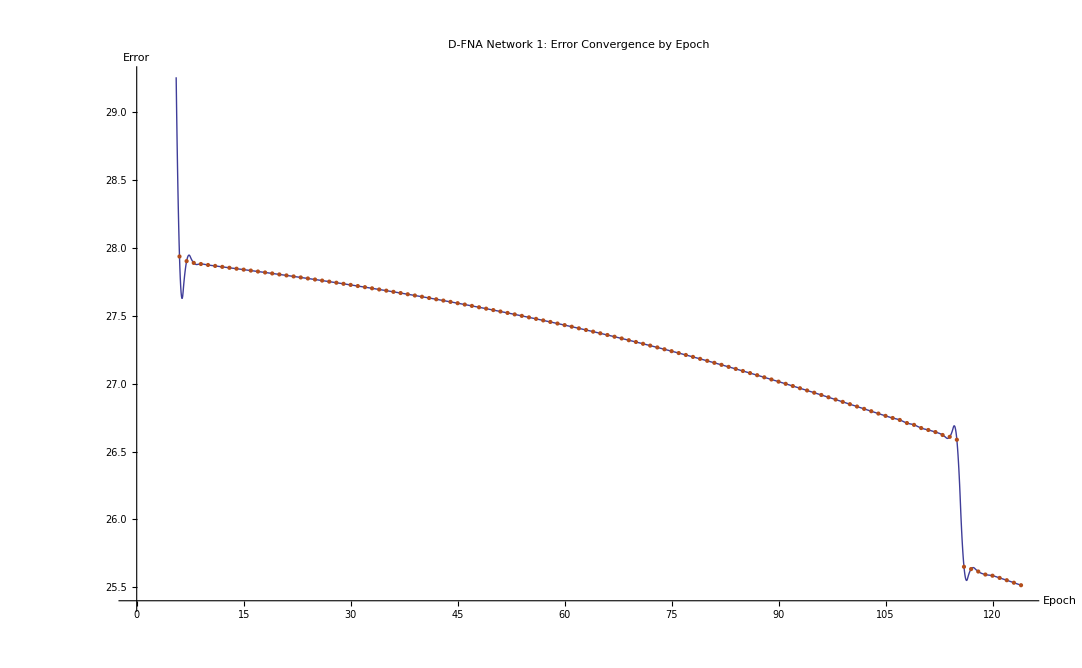

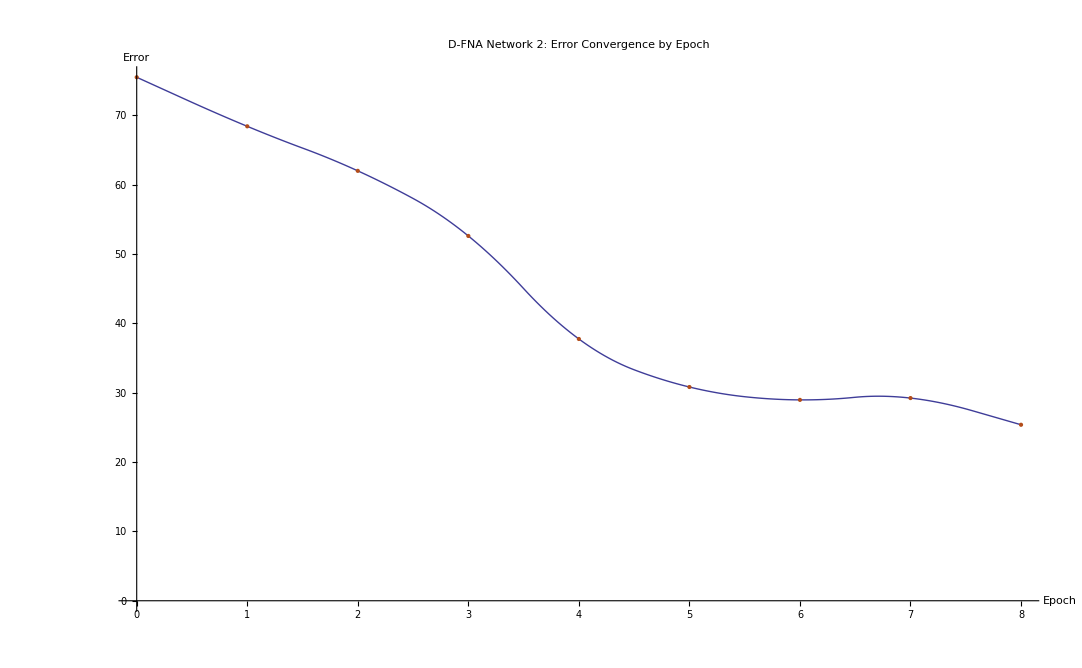

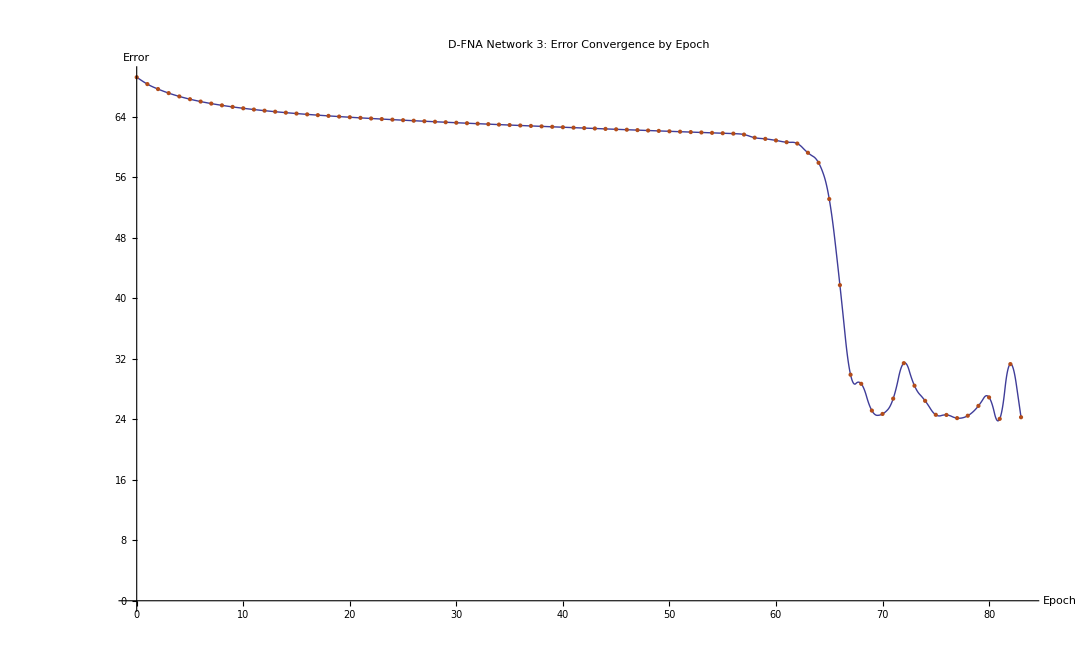

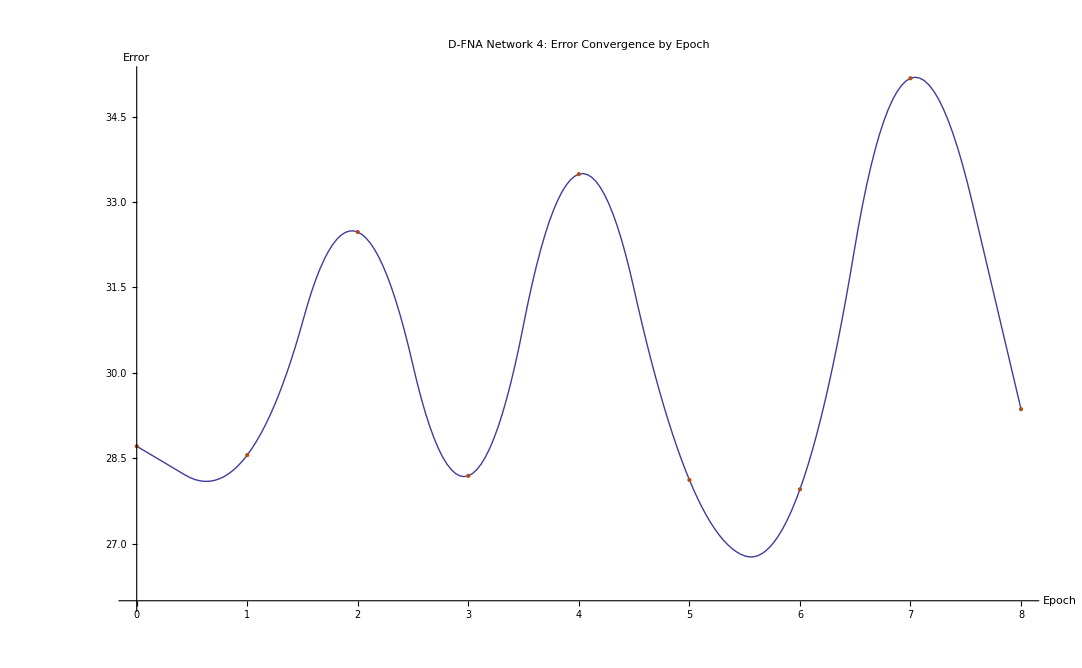

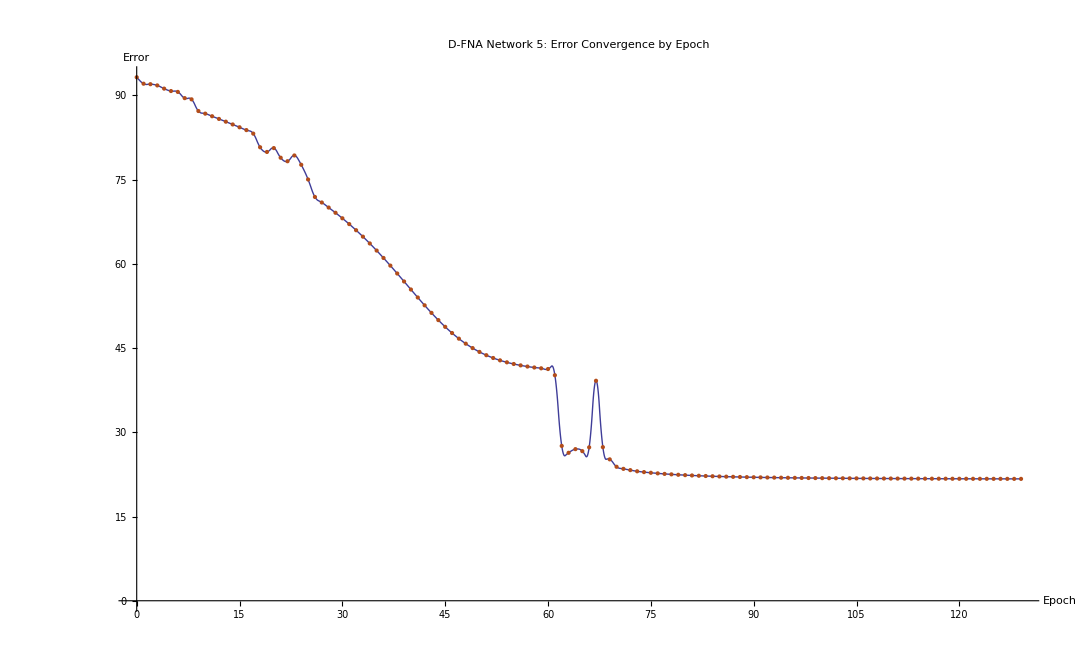

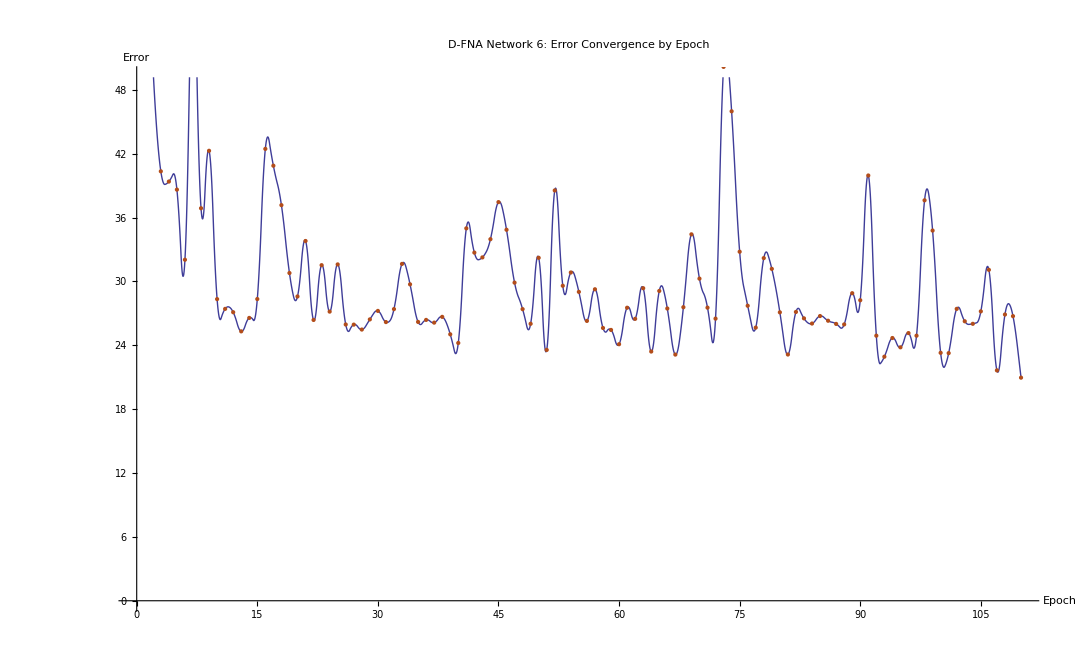

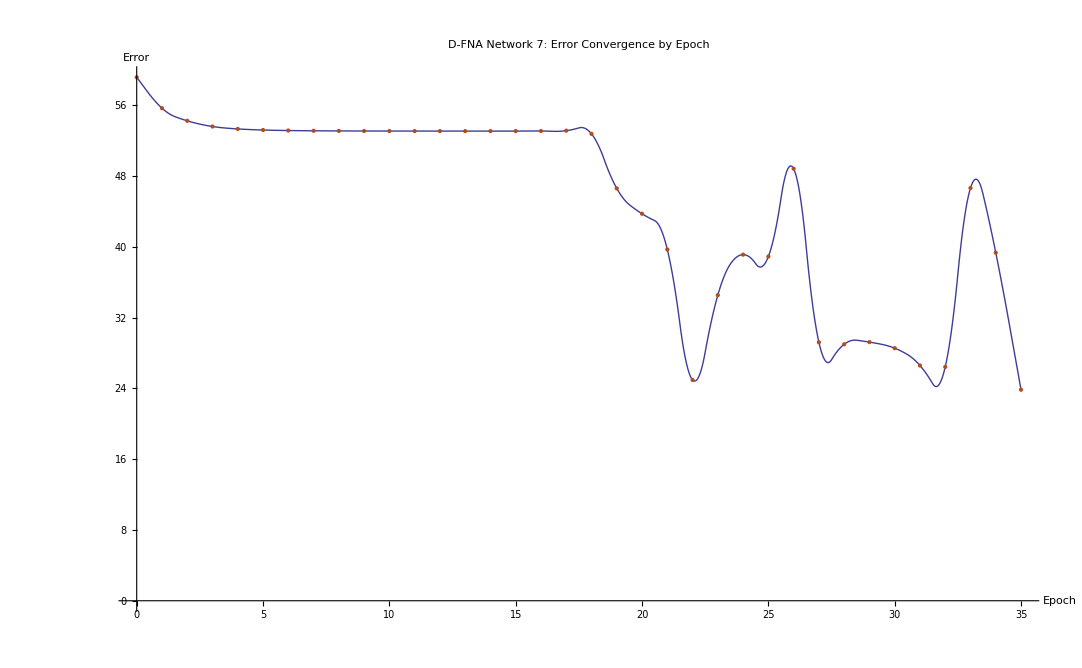

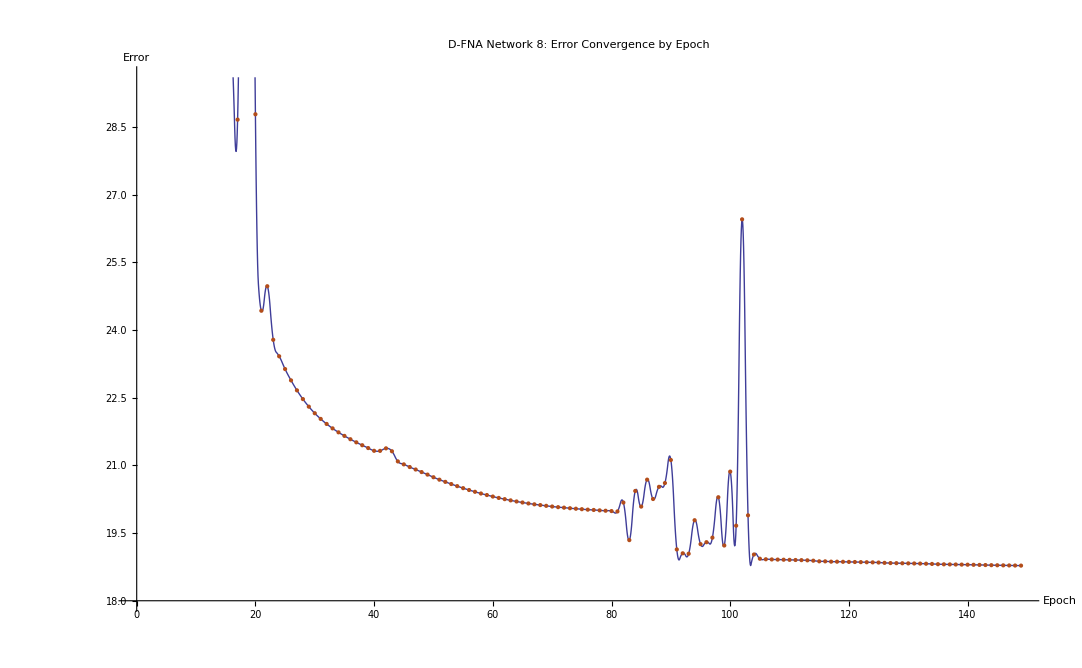

```mathematica
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\conclusion\\0.dat","Data"];
Show[ListLinePlot[data,InterpolationOrder->2],ListPlot[data,PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{Style["Epoch",FontSize->21],Style["Error",FontSize->21]},PlotLabel->Style["D-FNA Network 1: Error Convergence by Epoch",FontSize->36]]
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\conclusion\\1.dat","Data"];
Show[ListLinePlot[data,InterpolationOrder->2],ListPlot[data,PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{Style["Epoch",FontSize->21],Style["Error",FontSize->21]},PlotLabel->Style["D-FNA Network 2: Error Convergence by Epoch",FontSize->36]]
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\conclusion\\2.dat","Data"];
Show[ListLinePlot[data,InterpolationOrder->2],ListPlot[data,PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{Style["Epoch",FontSize->21],Style["Error",FontSize->21]},PlotLabel->Style["D-FNA Network 3: Error Convergence by Epoch",FontSize->36]]
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\conclusion\\3.dat","Data"];
Show[ListLinePlot[data,InterpolationOrder->2],ListPlot[data,PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{Style["Epoch",FontSize->21],Style["Error",FontSize->21]},PlotLabel->Style["D-FNA Network 4: Error Convergence by Epoch",FontSize->36]]
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\conclusion\\4.dat","Data"];
Show[ListLinePlot[data,InterpolationOrder->2],ListPlot[data,PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{Style["Epoch",FontSize->21],Style["Error",FontSize->21]},PlotLabel->Style["D-FNA Network 5: Error Convergence by Epoch",FontSize->36]]
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\conclusion\\5.dat","Data"];
Show[ListLinePlot[data,InterpolationOrder->2],ListPlot[data,PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{Style["Epoch",FontSize->21],Style["Error",FontSize->21]},PlotLabel->Style["D-FNA Network 6: Error Convergence by Epoch",FontSize->36]]
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\conclusion\\6.dat","Data"];
Show[ListLinePlot[data,InterpolationOrder->2],ListPlot[data,PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{Style["Epoch",FontSize->21],Style["Error",FontSize->21]},PlotLabel->Style["D-FNA Network 7: Error Convergence by Epoch",FontSize->36]]
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\conclusion\\7.dat","Data"];
Show[ListLinePlot[data,InterpolationOrder->2],ListPlot[data,PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{Style["Epoch",FontSize->21],Style["Error",FontSize->21]},PlotLabel->Style["D-FNA Network 8: Error Convergence by Epoch",FontSize->36]]
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\conclusion\\8.dat","Data"];
Show[ListLinePlot[data,InterpolationOrder->2],ListPlot[data,PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{Style["Epoch",FontSize->21],Style["Error",FontSize->21]},PlotLabel->Style["D-FNA Network 9: Error Convergence by Epoch",FontSize->36]]
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\conclusion\\9.dat","Data"];
Show[ListLinePlot[data,InterpolationOrder->2],ListPlot[data,PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{Style["Epoch",FontSize->21],Style["Error",FontSize->21]},PlotLabel->Style["D-FNA Network 10: Error Convergence by Epoch",FontSize->36]]
```

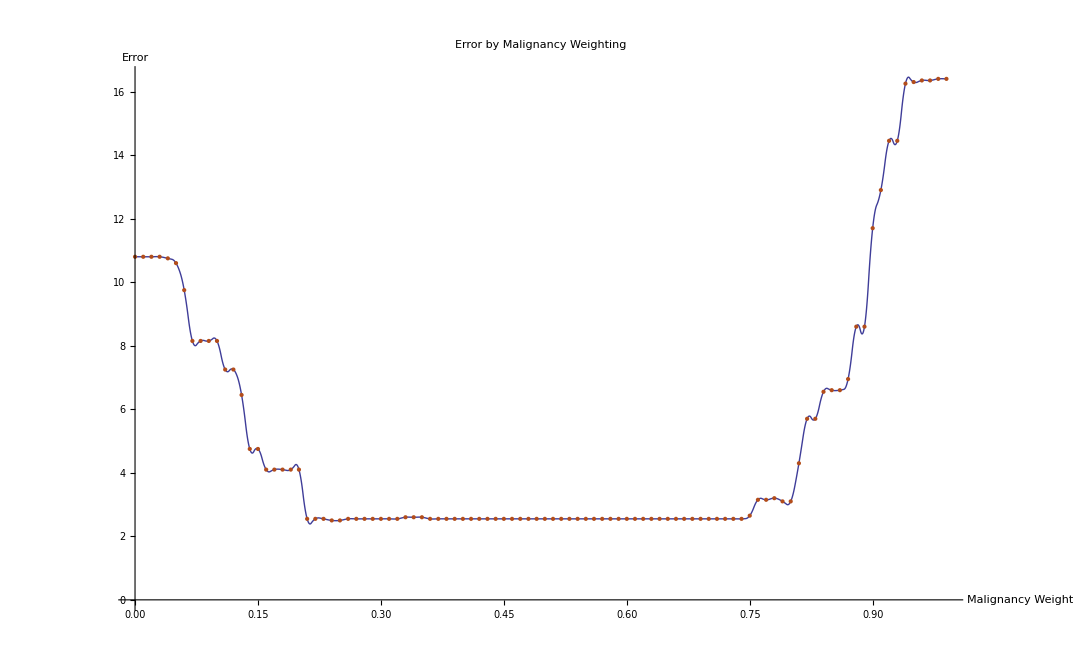

```mathematica
data = Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\step\\step.dat", "Data"];
Show[ListLinePlot[data,InterpolationOrder->2],ListPlot[data,PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{Style["Malignancy Weight",FontSize->21],Style["Error",FontSize->21]},PlotLabel->Style["Error by Malignancy Weighting",FontSize->36]]
```

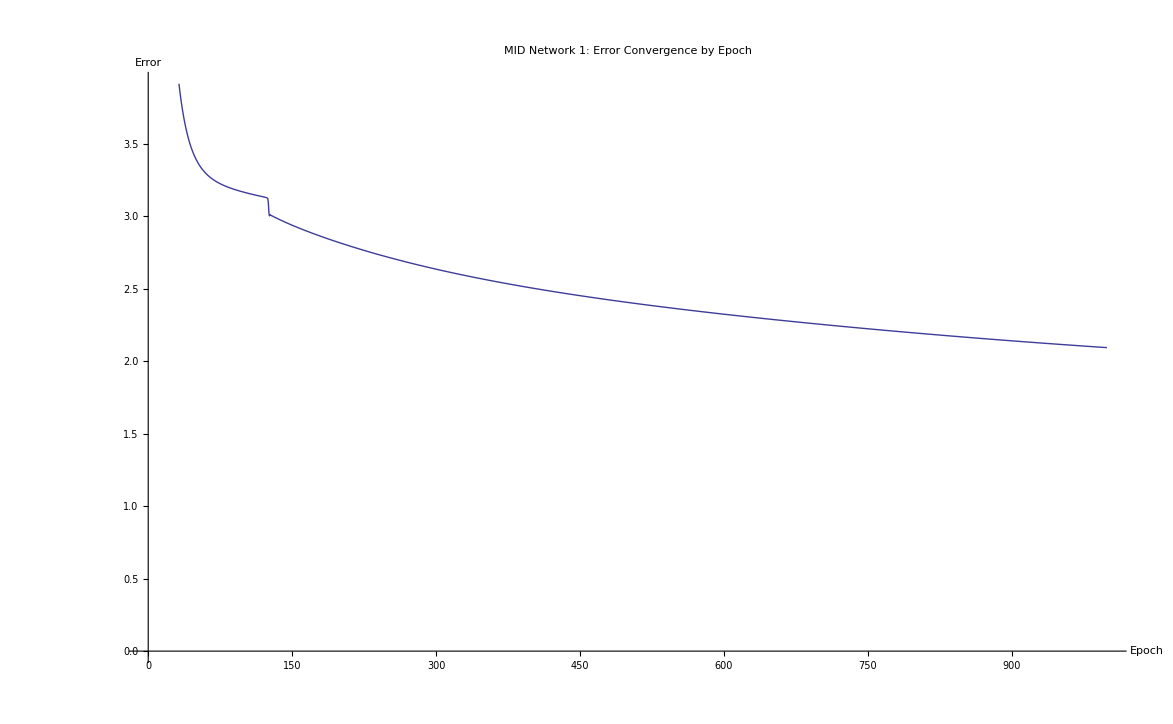

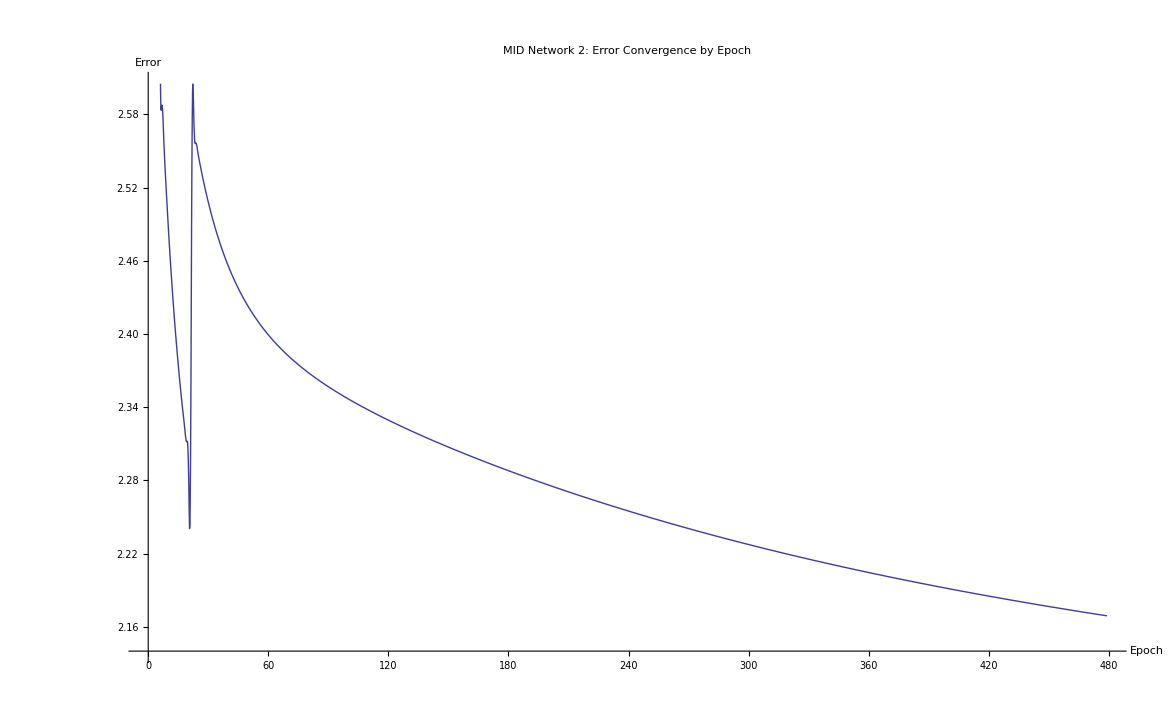

```mathematica
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\DATA\\EXPERIMENT\\OUTPUT\\IMAGES\\1\\convergence.dat","Data"];
Show[ListLinePlot[data,InterpolationOrder->2],AxesLabel->{Style["Epoch",FontSize->21],Style["Error",FontSize->21]},PlotLabel->Style["MID Network 1: Error Convergence by Epoch",FontSize->36]]
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\DATA\\EXPERIMENT\\OUTPUT\\IMAGES\\2\\convergence.dat","Data"];
Show[ListLinePlot[data,InterpolationOrder->2],AxesLabel->{Style["Epoch",FontSize->21],Style["Error",FontSize->21]},PlotLabel->Style["MID Network 2: Error Convergence by Epoch",FontSize->36]]
```